```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
<<Notation`
```

```mathematica
(* Simplify the notation for the formulas: index vectors based on a subscript notation *)
Notation[Subscript[x_, n_] ⟺ x_[[n_]]]
```

```mathematica
χ[a_?NumericQ]:=Exp[-a r^2]Sqrt[a/π];
α={0.298073,1.242567,5.782948,38.474970};
```

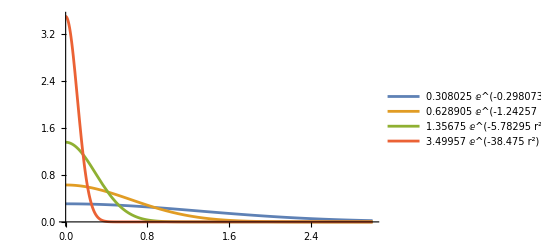

```mathematica
Plot[Array[χ[Subscript[α, #]]&,{4}]//Evaluate,{r,0,3},PlotLegends->"Expressions",PlotRange->All]
```

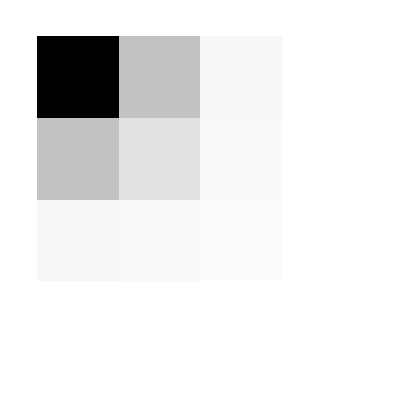
{True,-Graphics-,(12.0975 | 2.91188 | 0.37133 | 0.0230638
2.91188 | 1.42135 | 0.299025 | 0.022246
0.37133 | 0.299025 | 0.141565 | 0.018912
0.0230638 | 0.022246 | 0.018912 | 0.00824921)}

```mathematica
S=Array[(π/(Subscript[α, #1]+Subscript[α, #2]))^(3/2)&,{4,4}];
#[S]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

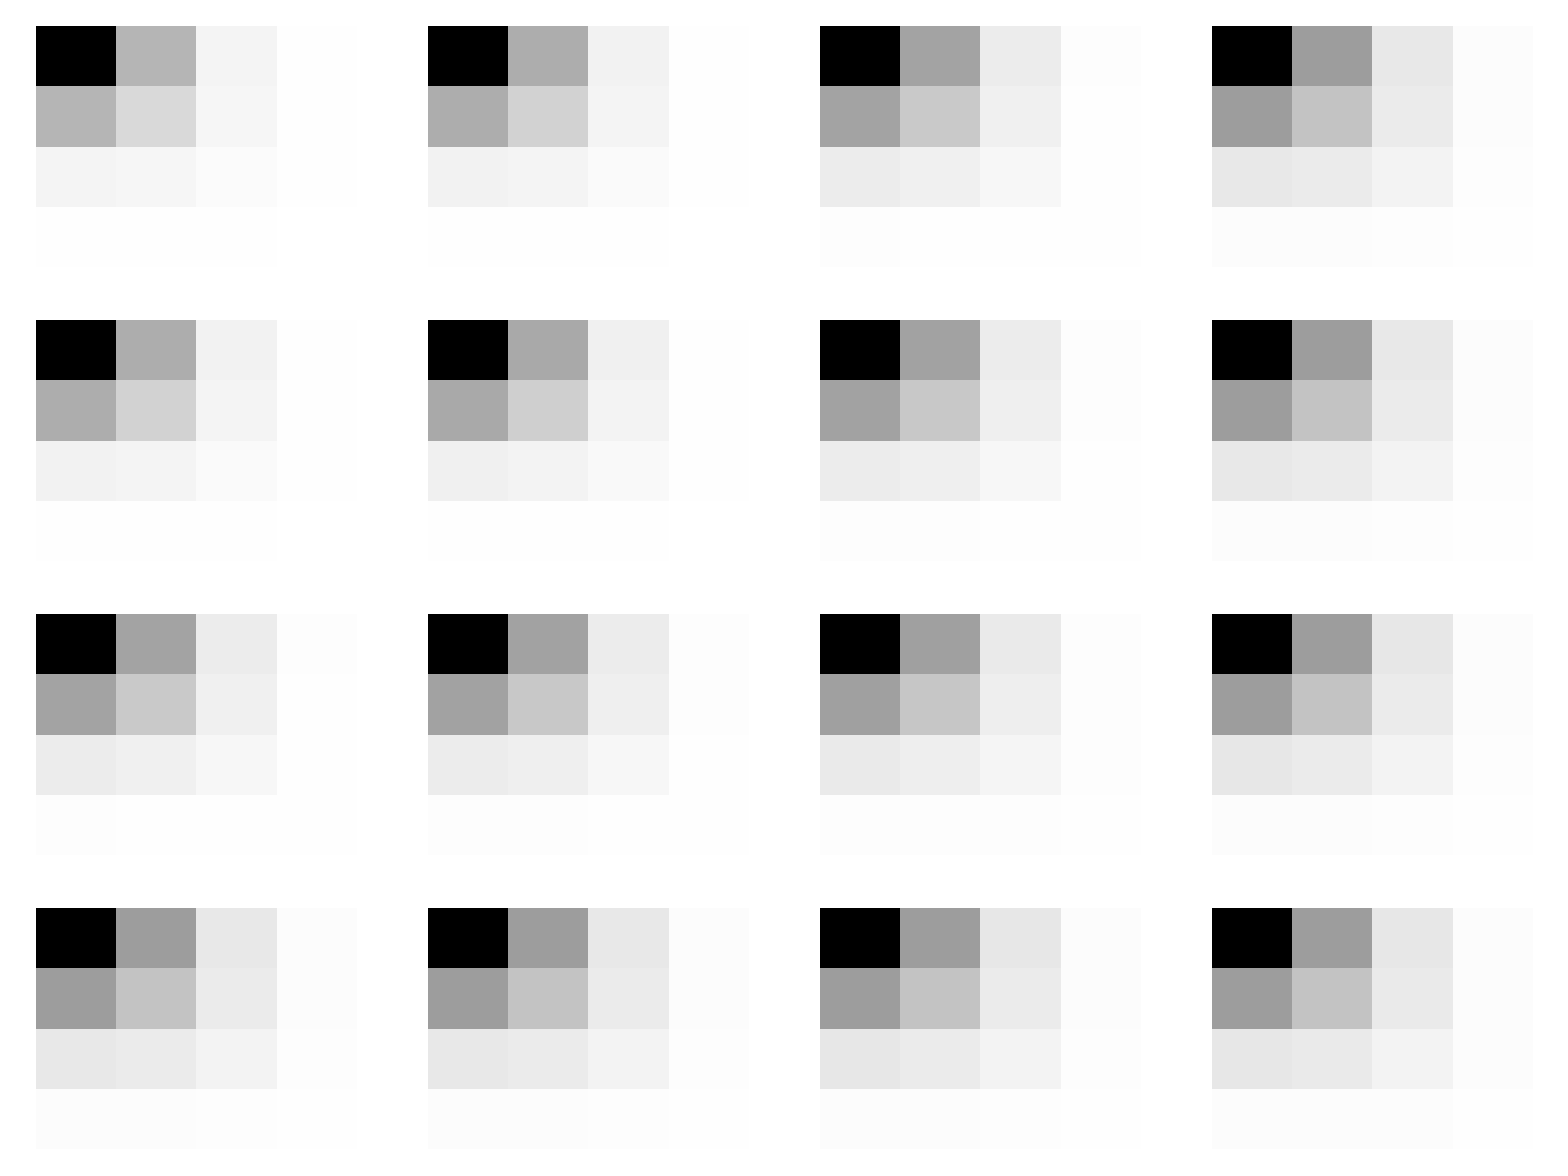
{False,-Graphics-,((90.1588 | 26.0598 | 3.7349 | 0.241237
26.0598 | 13.4535 | 3.02586 | 0.232725
3.7349 | 3.02586 | 1.45502 | 0.197998
0.241237 | 0.232725 | 0.197998 | 0.0866092) | (26.0598 | 8.39724 | 1.3527 | 0.092246
8.39724 | 4.55438 | 1.10442 | 0.0890156
1.3527 | 1.10442 | 0.542351 | 0.0758205
0.092246 | 0.0890156 | 0.0758205 | 0.0333109) | (3.7349 | 1.3527 | 0.271299 | 0.0221563
1.3527 | 0.791016 | 0.226207 | 0.0214052
0.271299 | 0.226207 | 0.118417 | 0.0183225
0.0221563 | 0.0214052 | 0.0183225 | 0.0082054) | (0.241237 | 0.092246 | 0.0221563 | 0.0026428
0.092246 | 0.0565288 | 0.0189789 | 0.00256439
0.0221563 | 0.0189789 | 0.0109962 | 0.0022375
0.0026428 | 0.00256439 | 0.0022375 | 0.00109008)
(26.0598 | 8.39724 | 1.3527 | 0.092246
8.39724 | 4.55438 | 1.10442 | 0.0890156
1.3527 | 1.10442 | 0.542351 | 0.0758205
0.092246 | 0.0890156 | 0.0758205 | 0.0333109) | (13.4535 | 4.55438 | 0.791016 | 0.0565288
4.55438 | 2.54106 | 0.649788 | 0.0545635
0.791016 | 0.649788 | 0.324729 | 0.046527
0.0565288 | 0.0545635 | 0.046527 | 0.0205277) | (3.02586 | 1.10442 | 0.226207 | 0.0189789
1.10442 | 0.649788 | 0.189101 | 0.0183394
0.226207 | 0.189101 | 0.0998599 | 0.0157126
0.0189789 | 0.0183394 | 0.0157126 | 0.00706223) | (0.232725 | 0.0890156 | 0.0214052 | 0.00256439
0.0890156 | 0.0545635 | 0.0183394 | 0.00248848
0.0214052 | 0.0183394 | 0.0106354 | 0.00217198
0.00256439 | 0.00248848 | 0.00217198 | 0.00105984)
(3.7349 | 1.3527 | 0.271299 | 0.0221563
1.3527 | 0.791016 | 0.226207 | 0.0214052
0.271299 | 0.226207 | 0.118417 | 0.0183225
0.0221563 | 0.0214052 | 0.0183225 | 0.0082054) | (3.02586 | 1.10442 | 0.226207 | 0.0189789
1.10442 | 0.649788 | 0.189101 | 0.0183394
0.226207 | 0.189101 | 0.0998599 | 0.0157126
0.0189789 | 0.0183394 | 0.0157126 | 0.00706223) | (1.45502 | 0.542351 | 0.118417 | 0.0109962
0.542351 | 0.324729 | 0.0998599 | 0.0106354
0.118417 | 0.0998599 | 0.0543803 | 0.00914797
0.0109962 | 0.0106354 | 0.00914797 | 0.00417837) | (0.197998 | 0.0758205 | 0.0183225 | 0.0022375
0.0758205 | 0.046527 | 0.0157126 | 0.00217198
0.0183225 | 0.0157126 | 0.00914797 | 0.00189851
0.0022375 | 0.00217198 | 0.00189851 | 0.000933125)
(0.241237 | 0.092246 | 0.0221563 | 0.0026428
0.092246 | 0.0565288 | 0.0189789 | 0.00256439
0.0221563 | 0.0189789 | 0.0109962 | 0.0022375
0.0026428 | 0.00256439 | 0.0022375 | 0.00109008) | (0.232725 | 0.0890156 | 0.0214052 | 0.00256439
0.0890156 | 0.0545635 | 0.0183394 | 0.00248848
0.0214052 | 0.0183394 | 0.0106354 | 0.00217198
0.00256439 | 0.00248848 | 0.00217198 | 0.00105984) | (0.197998 | 0.0758205 | 0.0183225 | 0.0022375
0.0758205 | 0.046527 | 0.0157126 | 0.00217198
0.0183225 | 0.0157126 | 0.00914797 | 0.00189851
0.0022375 | 0.00217198 | 0.00189851 | 0.000933125) | (0.0866092 | 0.0333109 | 0.0082054 | 0.00109008
0.0333109 | 0.0205277 | 0.00706223 | 0.00105984
0.0082054 | 0.00706223 | 0.00417837 | 0.000933125
0.00109008 | 0.00105984 | 0.000933125 | 0.000476287))}

```mathematica
Q=Array[(2 π^(5/2))/((Subscript[α, #1]+Subscript[α, #2])(Subscript[α, #3]+Subscript[α, #4])√(Subscript[α, #1]+Subscript[α, #2]+Subscript[α, #3]+Subscript[α, #4]))&,{4,4,4,4}];
{SymmetricMatrixQ[Q],Grid@Array[ArrayPlot[Subscript[Q, #1,#2],ImageSize->Tiny]&,{4,4}],MatrixForm@Q}
```

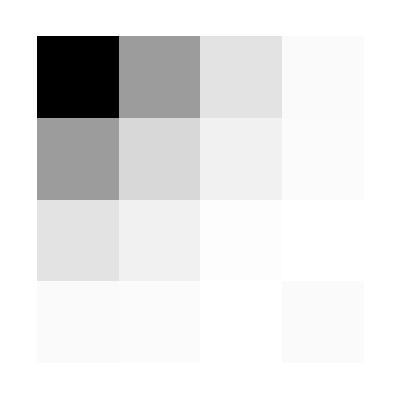
{True,-Graphics-,(-15.6704 | -6.05651 | -1.75072 | -0.303635
-6.05651 | -2.40744 | -0.871147 | -0.236062
-1.75072 | -0.871147 | 0.141492 | 0.00129568
-0.303635 | -0.236062 | 0.00129568 | 0.312776)}

```mathematica
H=Array[(3 π^(3/2) Subscript[α, #1] Subscript[α, #2])/(Subscript[α, #1]+Subscript[α, #2])^(5/2)-(4π)/(Subscript[α, #1]+Subscript[α, #2])&,{4,4}];
#[H]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

```mathematica
matNorm[v_,M_]:=v/Sqrt[v.M.v]
```

```mathematica
oldC=matNorm[ConstantArray[2.,{4}],S]
oldC.S.oldC
```

{0.218418,0.218418,0.218418,0.218418}

1.

```mathematica
diffNormList={}; (* List of the norm of the differences *)
```

```mathematica
prec=10^-6;(* Convergence precision *)
newC=oldC+prec;

While[Norm[oldC-newC]>prec,
AppendTo[diffNormList,Norm[oldC-newC]]; (* Append the norm of the difference to the diffNormList list *)
oldC=newC;(* Overwrite the previous eigenvalues *)
F=H+Q.oldC.oldC; (* Calculate the matrix F each iteration *)
{evals,efns}=Eigensystem[{F,S}];
{evals,efns}={evals[[#]],efns[[#]]}&@Ordering[evals]; (* Order the eigenvalues always in the same way for correctness *)
newC=matNorm[First@efns,S]; (* Normalize the minimal eigenvector w.r.t. the overlap matrix S *)
If[newC.S.newC!=1,Abort[],Nothing];(* Perform a numerical divergence check *)
]
```

```mathematica
groundEn=Quantity[2 H.oldC.oldC+Q.oldC.oldC.oldC.oldC,"HartreeEnergy"] (* Ground energy in Hartree energies *)
Abs[(groundEn-Quantity[-2.903, "HartreeEnergy"])/Quantity[-2.903, "HartreeEnergy"]]//PercentForm
```

-2.85516 E_h

1.648%

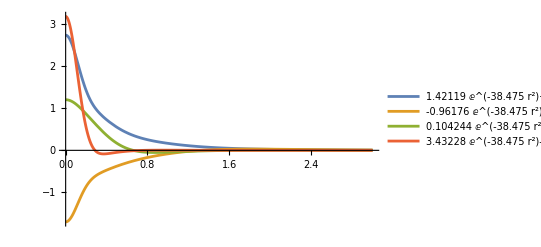

```mathematica
fns=#.Array[χ[Subscript[α, #]]&,{4}]&/@efns;
Plot[fns,{r,0,3},PlotRange->Full,PlotLegends->Placed["Expressions", Below]]
```

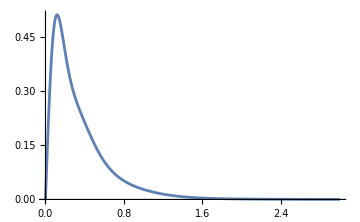

```mathematica
Plot[r Abs[First@fns]^2,{r,0,3},PlotRange->Full]
```

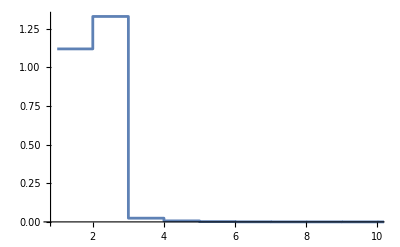

```mathematica
ListStepPlot[Drop[diffNormList,1],PlotRange->Full] (* Measurements give 0.05 seconds for the convergence time for an SCF loop *)
```